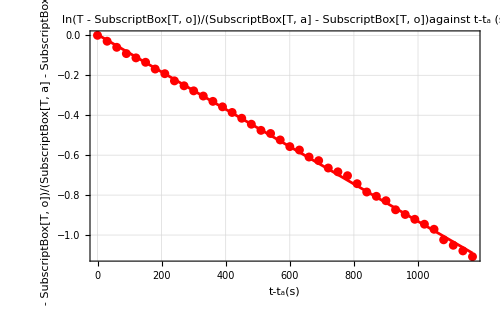
-Graphics-
Linear equation: y==0.00390156-0.000935358 x, Uncertainty in Slope: 4.15843×10^-6

```mathematica
(*Define the datasets*)
t1={{0,0},{30,-0.02956},{60,-0.06002},{90,-0.09143},{120,-0.11294},{150,-0.13492},{180,-0.16882},{210,-0.19208},{240,-0.22801},{270,-0.25270},{300,-0.27802},{330,-0.30400},{360,-0.33066},{390,-0.35806},{420,-0.38623},{450,-0.41522},{480,-0.44507},{510,-0.47585},{540,-0.49159},{570,-0.52386},{600,-0.55719},{630,-0.57429},{660,-0.60938},{690,-0.62740},{720,-0.66444},{750,-0.68349},{780,-0.70290},{810,-0.74291},{840,-0.78458},{870,-0.80609},{900,-0.82807},{930,-0.87353},{960,-0.89706},{990,-0.92116},{1020,-0.94585},{1050,-0.97117},{1080,-1.02381},{1110,-1.05121},{1140,-1.07938},{1170,-1.10837}};

(*Fit linear models to the data*)
fitt1=LinearModelFit[t1,x,x];

(*Extracting uncertainties in the slope of each fit*)uncertainty1=fitt1["ParameterTableEntries"][[2,2]];

(*Extract equations as strings*)
eq1=ToString[TraditionalForm[y==fitt1["BestFit"]]];

(*Existing code for plotting*)Column[{combinedPlot=Show[ListPlot[{t1},PlotStyle->{Red}],Plot[{fitt1[x]},{x,0,1170},PlotStyle->{Red}],Frame->True,FrameLabel->{"t-t_a(s)","ln(T - SubscriptBox[T, o])/(SubscriptBox[T, a] - SubscriptBox[T, o])"},GridLines->Automatic,PlotLabel->" ln(T - SubscriptBox[T, o])/(SubscriptBox[T, a] - SubscriptBox[T, o])against t-t_a (s)",ImageSize->500];
(*Displaying the results*)Column[{combinedPlot,Row[{"Linear equation: ",eq1,", Uncertainty in Slope: ",uncertainty1}]}]
}
]
```